# Biology 101 - Lesson 02: New Kind of Science

## Willem Nielsen

### Biology in New Kind of Science

Once Stephen discovered Rule 30, the connection to biology was quite straightforward (in retrospect at least); Given that simple programs could produce infinite complexity, Stephen speculated that much of the complex phenomena in biology was not a result of meticulous natural selection, but rather just a result of the fact that complexity was easy to generate.

The most striking example from New Kind of Science is in pigmentation patterns.

Pigmentation patterns of mollusk shells for example, in most species, are not exposed during the organisms lifetime and therefore have no effect on their fitness. But as you can see, from the array of shell images below, the patterns are very complex and look remarkably similar to the behavior of cellular automata.

-Graphics-

Here are some examples of similar cellular automata for comparison:

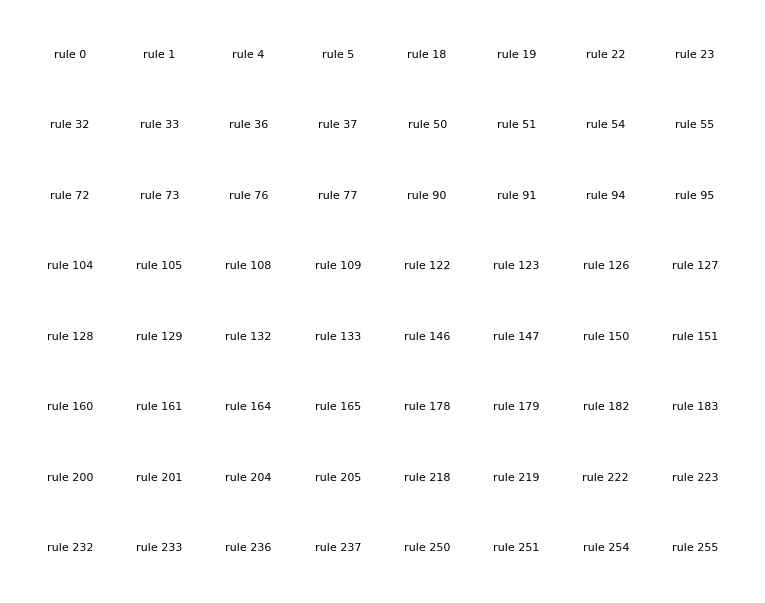

```mathematica
With[{srules=FromDigits[#,2]&/@Cases[Table[IntegerDigits[n,2,8],{n,0,255}],{_,a_,_,b_,a_,_,b_,_}],trand=BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,50]]},GraphicsGrid[Partition[Labeled[RulePlot[CellularAutomaton[#],trand,30,PlotRangePadding->None,ImageSize->90],Text[Style["rule "<>IntegerString[#],Italic]]]&/@srules,8],ImageSize->800]]
```

So what this example makes obvious, is that behaviors in biological systems aren’t always the result of natural selection: because the pigmentation patterns aren’t visible during the mollusc’s lifetime, we know there is no way of selection acting on them. Clearly, the complexity comes simply as a side-effect of the system responsible for generating pigmentation. And in fact, just like a cellular automata, mollusk shells can only grow on their edge, or “one line at a time”, further suggesting that the biological patterns can indeed be modeled by these simple programs.

But okay, is this true for pigmentation in general, or just for mollusks?

Looking at other species, we can see that these automaton-like pigmentation patterns are not at all unique to molluscs:

And in fact, Stephen shows that one can imitate many of these pigmentation patterns using simple programs:

```mathematica
Layer[n_]:=Layer[n]=Select[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],MemberQ[#,n|-n]&]

Layer[n_,1]:=Layer[n,1]=Cases[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],{_,n|-n}]

Layer[n_,2]:=Layer[n,2]=Complement[Layer[n],Layer[n,1]]

SpotStep[w_List?VectorQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i]]Total[RotateLeft[list,#]&/@Layer[i]],{i,0,Length[w]-1}],{2}]

SpotStep[w_List?MatrixQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i,j]]Total[RotateLeft[list,#]&/@Layer[i,j]],{i,0,Length[w]-1},{j,2}],{2}]

SpotEvolveList[w_List,list_,n_]:=NestList[SpotStep[w,#]&,list,n]

GraphicsGrid[Table[MapIndexed[ArrayPlot[#1,FrameLabel->{None,Text[Style["step "<>Apply[IntegerString,#2],Italic]]}]&,SpotEvolveList[rule,BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,{60,60}]],6]],{rule,{{1,1,-0.4,-0.4},{1,1,-0.2,-0.2}}}],ImageSize->700]
```

-Graphics-

```mathematica
Layer[n_]:=Layer[n]=Select[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],MemberQ[#,n|-n]&]

Layer[n_,1]:=Layer[n,1]=Cases[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],{_,n|-n}]

Layer[n_,2]:=Layer[n,2]=Complement[Layer[n],Layer[n,1]]

SpotStep[w_List?VectorQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i]]Total[RotateLeft[list,#]&/@Layer[i]],{i,0,Length[w]-1}],{2}]

SpotStep[w_List?MatrixQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i,j]]Total[RotateLeft[list,#]&/@Layer[i,j]],{i,0,Length[w]-1},{j,2}],{2}]

SpotEvolveList[w_List,list_,n_]:=NestList[SpotStep[w,#]&,list,n]

GraphicsGrid[Table[MapIndexed[ArrayPlot[#1,FrameLabel->{None,Text[Style["step "<>Apply[IntegerString,#2],Italic]]}]&,SpotEvolveList[rule,BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,{60,60}]],6]],{rule,{{{1,1},{1,1},{-0.4,0},{-0.4,0}},{{1,1},{1,1},{0,-0.6},{0,-0.6}}}}],ImageSize->700]
```

-Graphics-

The above pictures show four evolutions of a 2D cellular automata. The first two rows use the same rule starting from slightly different random initial conditions. The second two rows use rules with different horizontal and vertical weights. The variation in the patterns here is remarkably similar to those we just saw in biology. This makes clear the idea that the variation observed in different pigmentation patterns can result from small changes to simple programs.

So okay, the complex pigmentation patterns in biology seem to be a side-effect of the simple programs that generate pigmentation.

But how do we know for sure that these complex pigmentation patterns aren’t a result of some careful evolutionary process?

To test this, Stephen looks at constraint satisfaction problems, in an attempt to evolve to some particular pattern. As an example we can try to reach the constraint that every black cell should have exactly one neighbor; The pattern shown below, together with its rotations and reflections, is the only one that satisfies this constraint:

```mathematica
CloudGet["https://wolfr.am/nks-page0211b-graphic"]
```

-Graphics-

The “evolution” starts with a random grid of cells, a single cell chosen randomly, is reversed, if that cell does satisfy the local-constraint, then that change is kept, if it doesn’t then it is “rejected”. Here we show a few successive changes that were kept:

```mathematica
ConstraintViolations[array_]:=Count[Partition[array,{3,3},1],{{_,a_,_},{b_,x_,c_},{_,d_,_}}/;!(a+b+c+d==If[x==1,1,2]),{2}];
```

```mathematica
SeedRandom[3060];
arrs = Gather[NestList[With[{new=MapAt[1-#&,#,RandomInteger[{1,10},2]]},If[ConstraintViolations[new]>ConstraintViolations[#],#,new]]&,RandomChoice[{1,0},{10,10}],1000]];
```

```mathematica
pos = SparseArray[#]["ExplicitPositions"]&/@ Subtract@@@Partition[arrs[[All, 1]], 2, 1];
```

```mathematica
reps = MapThread[ReplacePart[#1, Thread[#2->Red]]&, {arrs[[2;;,1]], pos}];
```

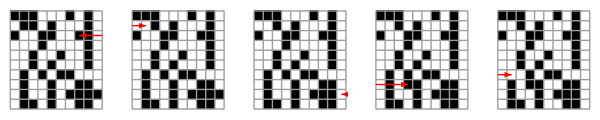

```mathematica
GraphicsRow[MapThread[{{"[◼]", "PerturbedArrayPlot"}}[#1, #2, "ArrowStyle"->Directive[Haloing[White],Arrowheads[.1]]]&,{arrs[[2;;6, 1]],pos[[;;5]]}], ImageSize->{600, Automatic}]
```

And here is our “loss curve”, or how many cells don’t satisfy the constraints:

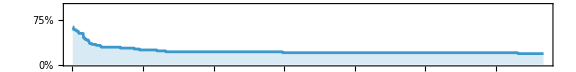

```mathematica
SeedRandom[3060];
ListLinePlot[ConstraintViolations/@NestList[With[{new=MapAt[1-#&,#,RandomInteger[{1,10},2]]},If[ConstraintViolations[new]>ConstraintViolations[#],#,new]]&,RandomChoice[{1,0},{10,10}],1000],Sequence[AspectRatio->1/8,PlotRange->{All,{0,65}},Filling->Axis,Frame->True,PlotRangePadding->0,ImageSize->Large,FrameTicks->{{Table[{n,Style[StringTemplate["``%"][100 (n/64)]]},{n,0,64,16}],False},{Automatic,False}}]]
```

So clearly we are making some progress towards satisfying the constraint, but how close do we get to the actual pattern?

Running this algorithm for many more steps and looking at snapshots along the way, we can see in the end the resulting pattern still doesn’t really look like the target pattern:

```mathematica
CloudGet["https://wolfr.am/nks-page0345a-graphic"]
```

-Graphics-

The problem, as Stephen explains, is that evolutionary algorithms tends to get stuck at local minima. Because the landscape for navigating these complex discrete systems is relatively rough, the algorithm will inevitably get stuck before it reaches some specific detailed pattern:

```mathematica
CloudGet["https://wolfr.am/nks-page0346b-graphic"]
```

-Graphics-

But can you get around this?

If you “relax the evolution”, by injecting some randomness into the search, Stephen finds that the iterative procedures end up with better results, but often only after an enormous amount of steps that would be infeasible for evolution.

And the takeaway here, is that evolution is limited in its ability to shape systems. This strongly suggests that the details of pigmentation patterns are not the result of some careful  evolutionary process, and their complexity is just a side-effect.

Now you may be thinking, “this pigmentation stuff is interesting, but what about other systems in biology?”

Well, one thing Stephen studies in NKS, is the shape of different organisms. In particular, he looks at the shapes of different leaves in the plant kingdom.

```mathematica
CloudGet["https://wolfr.am/nks-page0403a-graphic"]
```

-Graphics-

And what he finds is that the variation and complexity of leaf shape, can be also be modeled by changes to simple programs, in this case, substitution programs with slightly different branching radii:

```mathematica
GraphicsColumn[GraphicsRow[Flatten@{Graphics[{Line[#[[1]]],With[{head=#[[1,1,2]]},{Disk[head,.1],Arrowheads[.125,1.5],Arrow[{{head[[2]]-.4,head[[2]]},{head[[2]]+.4,head[[2]]}}]}],Translate[{Line[Flatten[#[[1;;2]],1]],Disk[#,.1]&/@#[[2,All,2]]},{2.5,0}]},Sequence[ImageSize->{Automatic,40},Frame->True,FrameTicks->False,FrameStyle->AbsoluteThickness[1],PlotRange->{{-0.75,3.4},{-0.25,2.25}}]]&@#[[4]],Graphics[{AbsoluteThickness[.3],Line/@#},Sequence[Frame->True,FrameTicks->False,PlotRange->All,PlotRangePadding->Scaled[0.05],FrameStyle->AbsoluteThickness[1]]]&/@#}&@With[{grow=#},Table[NestWhileList[Flatten[With[{head=#[[2]],dir=#[[2]]-#[[1]]},{head,head+#}&/@ReIm@grow[dir[[1]]+dir[[2]] I]]&/@#,1]&,{{{0,0},{0,1}}},(Length[#]<500&)],{θ,120 °,15 °,-15 °}]],ImageSize->{750,Automatic}]&/@Table[Function[Evaluate@Table[With[{t=θ ((2 i-2)/(Length[lengths]-1)-1)},# lengths[[i]] (Cos[t]+Sin[t] I)],{i,Length[lengths]}]],{lengths,{{.4,.7,.4},{.5,.4,.5},{.5,.5,.5},{.5,.6,.5},{.55,.8,.55},{.7,.8,.7},{.65,.6,.65},{.5,.6,.6,.5},{.65,.65}}}],ImageSize->Large]
```

-Graphics-

He then uses similar ideas to study animal growth and shape, in particular looking at the shapes of various shells. But the point is  that much like pigmentation, the observed variance and complexity in organism shape can mostly be explained not by natural selection, but rather by small changes in the underlying rules of simple programs.

To summarize the biological claims of NKS, we can imagine two views on biology. The first view, is that biological systems start as this simple goop. And evolution, is an adept and sober “sculptor”, meticulously removing bits of goop into these very specific shapes and patterns, that are chosen, because they are somehow more fit.

An alternative view, is that instead, biological systems, from the start are this complex amalgamation of parts that are capable of a wide range of different behaviors. And evolution is like a drunk, blindfolded sculptor, that is just doing its best to keep the biological systems from devolving into chaos.

In the first “sober sculptor model”, the causality lies with evolution, and the observed phenomena can be traced back to natural selection. In the second “drunk sculptor model”, the causality mostly lies with the systems, and biological phenomena can be explained mostly by modeling the physical systems.

Especially when New Kind of Science was published, the sober sculptor view was popular among biologists, and so Stephen made a point to emphasize the drunk sculptor view.

To be clear though, even in the drunk sculptor view, evolution does have some effect, and Stephen is not saying that it doesn’t. But the crucial point, is its effects will be high-level and the intricate details of biological systems can better be explained by computational irreducibility then by natural selection.

In NKS though, Stephen did not actually have a minimal model for the evolution of adaptive systems. He touched on it with the constraint satisfaction problems, but critically, this was only really modeling the process of pigmentation, and there was no clear picture of a “computational organism”.

In recent times, Stephen has made progress on this front, and it is the critical new element in his view on biology.